```mathematica
NA=0.12;
a=4.5*10^-6/2;(*core radius*)
V[λ_]:=(2π)/λ a*NA;
MRadius[V_]:=a*(0.65+1.619/V^1.5+2.879/V^6-0.016-1.561*V^-7);
```

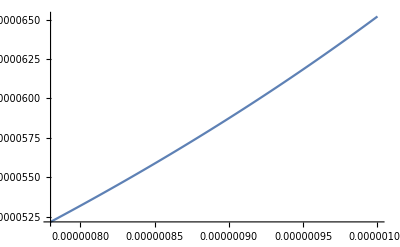

```mathematica
Plot[2*MRadius[V[λ]],{λ,780*10^-9,1000*10^-9}]
```

```mathematica
MRadius[V[947*10^-9]]
```

3.08246×10^-6